{{0,576},{1/2,8575/64},{1,0},{3/2,-1125/64},{2,-8},{5/2,-81/64},{3,0},{7/2,-5/64},{4,0},{9/2,63/64},{5,16}}

{{0,576},{1/2,8575/64},{1,0},{3/2,-1125/64},{2,-8},{5/2,-81/64},{3,0},{7/2,-5/64},{4,0},{9/2,63/64},{5,16}}

0. | 576.
0.5 | 133.984
1. | 0.
1.5 | -17.5781
2. | -8.
2.5 | -1.26563
3. | 0.
3.5 | -0.078125
4. | 0.
4.5 | 0.984375
5. | 16.

0.00 |        576.00
         0.50 |        133.98
         1.00 |          0.00
         1.50 |        -17.58
         2.00 |         -8.00
         2.50 |         -1.27
         3.00 |          0.00
         3.50 |         -0.08
         4.00 |          0.00
         4.50 |          0.98
         5.00 |         16.00

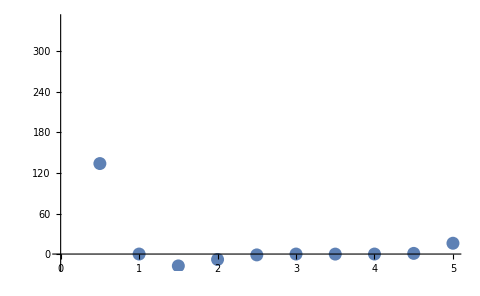

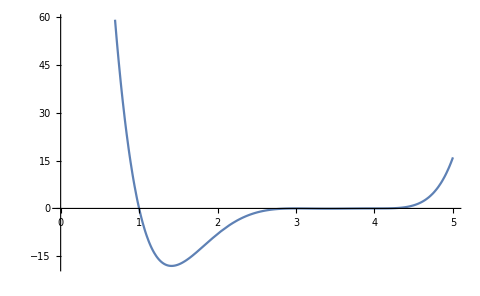

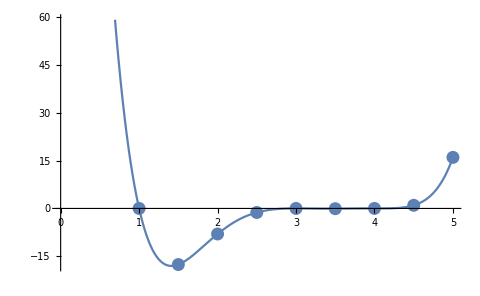

```mathematica
a=0;b=5;n=11;
h=(b-a)/(n-1);
f[x_]:=x^6-19*x^5+147 x^4-589 x^3+1276 x^2-1392 x+576
tab1=Table[{x=a+i*h,f[x]},{i,0,n-1}]
{{0,576},{1/2,8575/64},{1,0},{3/2,-(1125/64)},{2,-8},{5/2,-(81/64)},{3,0},{7/2,-(5/64)},{4,0},{9/2,63/64},{5,16}}
tab1=TableForm[N[tab1]]
PaddedForm[tab1,{11,2}]
gr1:=Plot[f[x],{x,a,b}];
gr2:=ListPlot[{{0,576},{1/2,8575/64},{1,0},{3/2,-(1125/64)},{2,-8},{5/2,-(81/64)},{3,0},{7/2,-(5/64)},{4,0},{9/2,63/64},{5,16}}]
Show[gr2]
Show[gr1]
Show[{gr1,gr2}]
```